```mathematica
Clear[p, k, L];
a=Exp[I p L/2];
b =Exp[I k L /2];
S={{a, 0, -1/b, -b},{-p a, 0, -k /b, k b},{0, a, -b, -1/b},{0,p a, -k b, k /b}};
y={-1/a,-p /a,0,0};
 LinearSolve[S, y]//FullSimplify
```

{(ⅇ^(-ⅈ L p) (-1+ⅇ^(2 ⅈ k L)) (-k^2+p^2))/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2),-(4 ⅇ^(ⅈ L (k-p)) k p)/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2),-(2 ⅇ^(1/2 ⅈ L (k-p)) p (k+p))/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2),(2 ⅇ^(1/2 ⅈ L (3 k-p)) p (-k+p))/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2)}

```mathematica
Clear[k,p,L];
(4 ⅇ^(ⅈ L (k-p)) k p)/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2)(4 ⅇ^(-ⅈ L (k-p)) k p)/(ⅇ^(-2 ⅈ k L) (k-p)^2-(k+p)^2)//FullSimplify
```

1/(Cos[k L]^2+((k^2+p^2)^2 Sin[k L]^2)/(4 k^2 p^2))

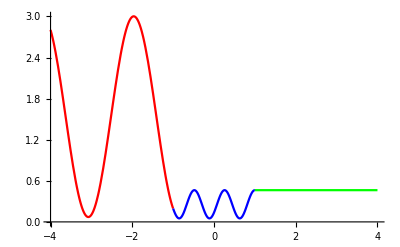

```mathematica
(*Assuming mu=hbar=1*)
L=2;
En=1;
V=8;
p=Sqrt[2En];
k=Sqrt[2(En+V)];
r=(ⅇ^(-ⅈ L p) (-1+ⅇ^(2 ⅈ k L)) (-k^2+p^2))/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2);
t=-(4 ⅇ^(ⅈ L (k-p)) k p)/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2);
A=-(2 ⅇ^(1/2 ⅈ L (k-p)) p (k+p))/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2);
B=(2 ⅇ^(1/2 ⅈ L (3 k-p)) p (-k+p))/(ⅇ^(2 ⅈ k L) (k-p)^2-(k+p)^2);
left=Plot[Abs[Exp[I p x]+r Exp[-I p x]]^2,{x,-2L,-L/2},PlotStyle->Red,PlotRange->Full];
middle=Plot[Abs[A Exp[I k x]+B Exp[-I k x]]^2,{x,-L/2,L/2},PlotStyle->Blue,PlotRange->Full];
right = Plot[Abs[t ]^2,{x,L/2,2L},PlotStyle->Green,PlotRange->Full];
Show[left, middle, right,PlotRange->{{-2L,2L},{0,3}}]
```

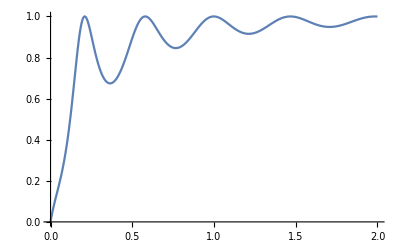

```mathematica
r= 10;
Plot[4u(1+u)/(Sin[2r Sqrt[1+u]]^2+4u(1+u)),{u,0,2},PlotRange->Full]
```

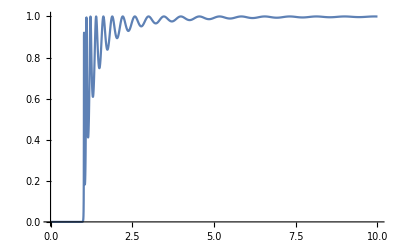

```mathematica
r=10;
Plot[1/(1+Sinh[2 r Sqrt[1-u]]^2/(4u(1-u))),{u,0,10},PlotRange->Full]
```